H(a)

```mathematica
(*Quit[]*)
```

```mathematica
?NSolve
```

NSolve[expr,vars] attempts to find numerical approximations to the solutions of the system expr of equations or inequalities for the variables vars. 
NSolve[expr,vars,Reals] finds solutions over the domain of real numbers.

```mathematica
OmegaM0=0.3111;
OmegaR0=10^(-5);
s=1
a=.
HoverH0equation=1-x^-2(OmegaM0/a+OmegaR0/a^2)-(a/x)^(2(1+s))(1-OmegaM0-OmegaR0);
Solution=NSolve[HoverH0equation==0,x]
a=1
Solution
```

1

{{x→-0.00223607 √(1/a^2+31110./a-(1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2)},{x→0.00223607 √(1/a^2+31110./a-(1. √(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2)},{x→-0.00223607 √(1/a^2+31110./a+(√(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2)},{x→0.00223607 √(1/a^2+31110./a+(√(1.+62220. a+9.67832×10^8 a^2+2.75556×10^10 a^8))/a^2)}}

1

{{x→0.-0.829994 ⅈ},{x→0.+0.829994 ⅈ},{x→-1.},{x→1.}}

```mathematica
a=.
sm0p5=(5.*10^-6 (69999. a^3+√(-400000. (-1.-30000. a) a^2+4.899860001*10^9 a^6)))/a^2
s0=(0.0031622776601683794 √(1.+30000. a+69999. a^4))/a
s0p5=-(1.2599210498948732 (-1.-30000. a))/((1.889973*^16 a^9+√(1.08*^17 (-1.-30000. a)^3 a^6+3.571997940729*^32 a^18))^(1/3))+1/a^2 2.645668419946999*^-6 (1.889973*^16 a^9+√(1.08*^17 (-1.-30000. a)^3 a^6+3.571997940729*^32 a^18))^(1/3)
s1=0.00223606797749979 √(1/a^2+30000./a+(√(1.+60000. a+9.*^8 a^2+2.79996*^10 a^8))/a^2)
HLCDM = Sqrt[OmegaM0/a+OmegaR0/a^2+a^2 *0.6889]
s1o5 =Root[-1.680579953429951*^24 a^12+(-1./a^10-150000./a^9-(9.*^9)/a^8-(2.7*^14)/a^7-(4.05*^18)/a^6-(2.43*^22)/a^5) #1^2+(500000./a^8+(6.*^10)/a^7+(2.7*^15)/a^6+(5.4*^19)/a^5+(4.05*^23)/a^4) #1^4+(-(1.*^11)/a^6-(9.*^15)/a^5-(2.7*^20)/a^4-(2.7*^24)/a^3) #1^6+((1.*^16)/a^4+(6.*^20)/a^3+(9.*^24)/a^2) #1^8+(-(5.*^20)/a^2-(1.5*^25)/a) #1^10+1.*^25 #1^12&,2]
```

(5.×10^-6 (69999. a^3+√(-400000. (-1.-30000. a) a^2+4.89986×10^9 a^6)))/a^2

(0.00316228 √(1.+30000. a+69999. a^4))/a

-(1.25992 (-1.-30000. a))/((1.88997×10^16 a^9+√(1.08×10^17 (-1.-30000. a)^3 a^6+3.572×10^32 a^18))^(1/3))+(2.64567×10^-6 (1.88997×10^16 a^9+√(1.08×10^17 (-1.-30000. a)^3 a^6+3.572×10^32 a^18))^(1/3))/a^2

0.00223607 √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)

√(1/(100000 a^2)+0.3/a+0.6889 a^2)

Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]

```mathematica
a=1

sm0p5
s0
s0p5
s1
HLCDM 
s1o5
```

1

1.

1.

1.

«1 more identical outputs»

0.99444

1.

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i. 
Plot[{…,w[f_i],…},…] plots f_i with features defined by the symbolic wrapper w.
Plot[…,{x}∈reg] takes the variable x to be in the geometric region reg.

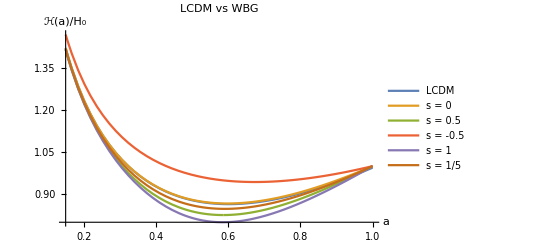

```mathematica
Plot[{HLCDM,s0,s0p5,sm0p5,s1,s1o5},{a,0.15,1}, PlotLegends->{"LCDM","s = 0","s = 0.5 ","s = -0.5 ","s = 1","s = 1/5 "}, AxesLabel->{Style["a",FontSize->20],Style["ℋ(a)/H_0",FontSize->20]},PlotLabel->Style["LCDM vs WBG", FontSize->30]]
```

```mathematica
s1/HLCDM
```

1.00559

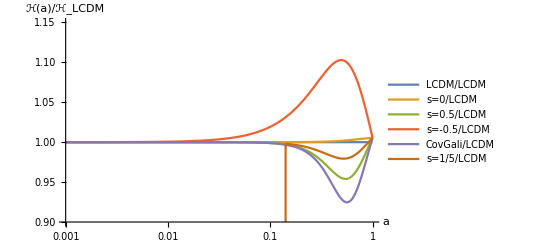

Null

```mathematica
LogLinearPlot[{HLCDM/HLCDM, s0/HLCDM, s0p5/HLCDM, sm0p5/HLCDM,s1/HLCDM,s1o5/HLCDM},{a,0.001,1}, PlotLegends->{"LCDM/LCDM","s=0/LCDM","s=0.5/LCDM ","s=-0.5/LCDM ","CovGali/LCDM","s=1/5/LCDM"}, AxesLabel->{Style["a",FontSize->20],Style["ℋ(a)/ℋ_LCDM",FontSize->20]},PlotLabel->Style[" ", FontSize->30], PlotRange->{{0.001,1},{0.9,1.15}}]
```

Let’s find X(a)

```mathematica
a=.
p=1
q=5/2
s = p/(2q)
XoverXds = (   (1-OmegaM0-OmegaR0)^( 1/(2(s+1)) ) s1^(-1) a )^(1/q)
```

1

5/2

1/5

10.824 (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^(2/5)

```mathematica
(*XLCDM = *)
Xs0 =69998.99999999997 (a^2/(√(1.+30000. a+69999. a^4)))^2.
Xs0p5 =0.7883660079734442 (a/(-(1.2599210498948732 (-1.-30000. a))/((1.889973*^16 a^9+√(1.08*^17 (-1.-30000. a)^3 a^6+3.571997940729*^32 a^18))^(1/3))+1/a^2 2.645668419946999*^-6 (1.889973*^16 a^9+√(1.08*^17 (-1.-30000. a)^3 a^6+3.571997940729*^32 a^18))^(1/3)))^2.
Xsm0p5=1.9599440004000008*^10 (a^3/(69999. a^3+√(-400000. (-1.-30000. a) a^2+4.899860001*^9 a^6)))^2.
Xs1 = 167330.81007393703 (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.*^8 a^2+2.79996*^10 a^8))/a^2)))^2.
Xs1o5 = 10.824004689806106 (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.*^8 a^2+2.79996*^10 a^8))/a^2)))^(2/5)
```

69999. (a^2/(√(1.+30000. a+69999. a^4)))^2.

0.788366 (a/(-(1.25992 (-1.-30000. a))/((1.88997×10^16 a^9+√(1.08×10^17 (-1.-30000. a)^3 a^6+3.572×10^32 a^18))^(1/3))+(2.64567×10^-6 (1.88997×10^16 a^9+√(1.08×10^17 (-1.-30000. a)^3 a^6+3.572×10^32 a^18))^(1/3))/a^2))^2.

1.95994×10^10 (a^3/(69999. a^3+√(-400000. (-1.-30000. a) a^2+4.89986×10^9 a^6)))^2.

167331. (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^2.

10.824 (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^(2/5)

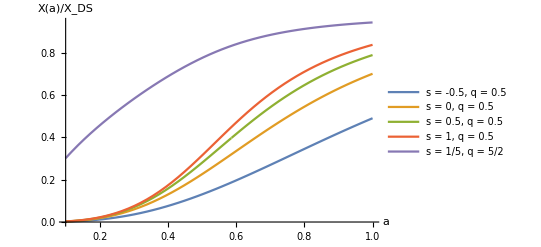

```mathematica
Plot[{Xsm0p5,Xs0,Xs0p5,Xs1,Xs1o5},{a,0.1,1}, PlotLegends->{"s = -0.5,  q = 0.5","s = 0,  q = 0.5 ","s = 0.5,  q = 0.5 ","s = 1,  q = 0.5","s = 1/5, q = 5/2"}, AxesLabel->{Style["a",FontSize->20],Style["Χ(a)/Χ_DS",FontSize->20]}]
```

lets calculate Phi prime

Covariant Galileon!

```mathematica
Chi =Xs1 
ConformalH = s1
Sqrt[-Chi]/ConformalH//PowerExpand//Simplify
Phiprime = Integrate[%,a]
Evaluate[%]
```

167331. (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^2.

0.00223607 √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)

((0.+182938. ⅈ) a^3.)/(1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))

(0.+182938. ⅈ) ∫a^3./(1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))ⅆa

(0.+182938. ⅈ) ∫a^3./(1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))ⅆa

```mathematica
?Evaluate
```

Evaluate[expr] causes expr to be evaluated even if it appears as the argument of a function whose attributes specify that it should be held unevaluated.

```mathematica
a=0.51
0.00223606797749979 √(1/a^2+30000/a+(√(1.+60000. a+9*10^8 a^2+2.79996*10^10 a^8))/a^2)
+0.00223606797749979 √(1/a^2+30000/a+(√(1.+60000. a+9*10^8 a^2+2.79996*10^10 a^8))/a^2)
a=.
```

0.51

0.812418

0.812418

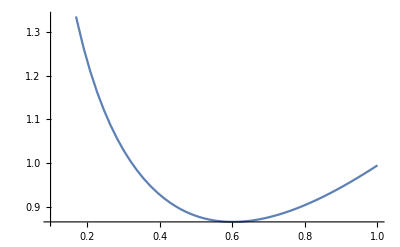

```mathematica
Plot[Sqrt[OmegaM0/a+OmegaR0/a^2+a^2 *0.6889],{a,0.1,1}]
```

EFT functions plots

```mathematica
DeSitterFP = {Subscript[c, 2]->3-6 Subscript[c, 4]-24 Subscript[c, 5]+12 Subscript[c, 4] p+24 Subscript[c, 4] q,Subscript[c, 3]->(√2 p)/(-1+2 p+2 q)-(4 √2 Subscript[c, 4] p)/(-1+2 p+2 q)-(16 √2 Subscript[c, 5] p)/(-1+2 p+2 q)+(8 √2 Subscript[c, 4] p^2)/(-1+2 p+2 q)-(4 √2 Subscript[c, 4] q)/(-1+2 p+2 q)-(16 √2 Subscript[c, 5] q)/(-1+2 p+2 q)+(24 √2 Subscript[c, 4] p q)/(-1+2 p+2 q)+(16 √2 Subscript[c, 4] q^2)/(-1+2 p+2 q)}
```

{c2→3+18. c4-24 c5,c3→0.707107+12.7279 c4-16.9706 c5}

covariant galileon

```mathematica
Omega=-1-2 (-1)^(-p-2 q) Subscript[c, 4] Subscript[χ, DS]^(-p-2 q) ℋ[a]^(2 (p+2 q)) φ'[a]^(2 (p+2 q))
```

-1-2 (-1)^(-p-2 q) c4 XDS^(-p-2 q) Hconf[a]^(2 (p+2 q)) Phi'[a]^(2 (p+2 q))

```mathematica
Subscript[χ, DS]=0.1
Subscript[χ, DS] = Subscript[χ, DS]
c4=1
c5= 0
```

0.1

0.1

1

0

```mathematica
ConformalH=s1//PowerExpand//Simplify
Chi = Xs1//PowerExpand//Simplify
CovariantGalileon={p->1,q->0.5,s->1,φ'[a]->Sqrt[-Chi]/ConformalH,ℋ[a]-> ConformalH}
PhiPrime[a]->Sqrt[-Chi]/ConformalH
```

0.00223607 √((1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)

(167331. a^4.)/(1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))

{1→1,0.5→0.5,1→1,Phi'[a]→(182938. √(-a^4./(1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))))/(√((1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)),Hconf[a]→0.00223607 √((1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)}

PhiPrime[a]→(182938. √(-a^4./(1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))))/(√((1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2))

```mathematica
OmegaCG=Omega/.DeSitterFP/.ȧ->ConformalH a/.CovariantGalileon/.Subscript[χ, DS]->0.5//PowerExpand//Simplify
```

-1-(5.59992×10^12 a^8.)/((1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))^2.)

```mathematica
OmegaCG/.a->1
```

-140.998

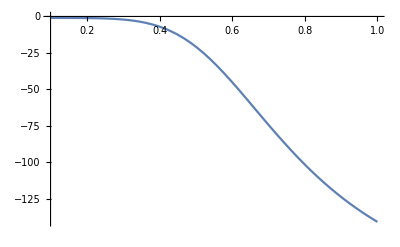

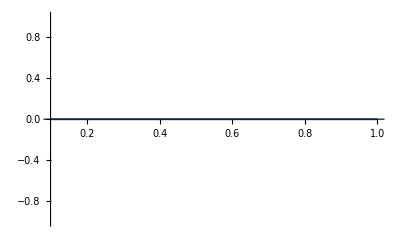

```mathematica
Plot[Re[OmegaCG],{a,0.1,1}]
Plot[Im[OmegaCG],{a,0.1,1}]
```

```mathematica
Subscript[χ, DS] = -0.010;
Subscript[χ, DS] = Subscript[χ, DS];
c4=.;
c5= 0;
p=1;
q=0.5;
s=1;
Omega=-1-2 (-1)^(-p-2 q) Subscript[c, 4] Subscript[χ, DS]^(-p-2 q) ℋ[a]^(2 (p+2 q)) φ'[a]^(2 (p+2 q))
ConformalH=s1//PowerExpand//Simplify;
Chi = Xs1//PowerExpand//Simplify;
CovariantGalileon={p->1,q->0.5,s->1,φ'[a]->Sqrt[-Chi]/ConformalH,ℋ[a]-> ConformalH};
OmegaCG=Omega/.DeSitterFP/.ȧ->ConformalH a/.CovariantGalileon/.Subscript[χ, DS]->0.5//PowerExpand//Simplify
OmegaCG/.a->1
OmegaCG/.a->0.1
Plot[Re[OmegaCG],{a,0.1,1}]
Plot[Im[OmegaCG],{a,0.1,1}]
```

-1-(20000.+4.89859×10^-12 ⅈ) c4 Hconf[a]^4. Phi'[a]^4.

-1-(5.59992×10^14 a^8. c4)/((1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))^2.)

-1-13999.8 c4

-1-0.155447 c4

-Graphics-

-Graphics-

```mathematica
OmegaXDSm1 = 0.5-(1.3999799999999989*^10+6.85792410348124*^-6 ⅈ) a^8. (1.+30000. a+1. √(1.+60000. a+9.*^8 a^2+2.79996*^10 a^8))^1.;

OmegaXDSm10 =-1-(5.599919999999994*^8 a^8.)/((1.+30000. a+1. √(1.+60000. a+9.*^8 a^2+2.79996*^10 a^8))^2.)
```

-1-(5.59992×10^8 a^8.)/((1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))^2.)

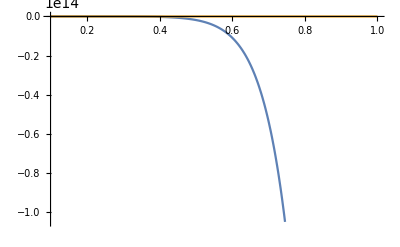

-Graphics-

```mathematica
Plot[{Re[OmegaXDSm1],Re[OmegaXDSm10]},{a,0.1,1}]
Plot[Im[OmegaCG],{a,0.1,1}]
```

```mathematica
L = 1/(a^2 ȧ)(-1)^(-p-2 q) Subscript[m, p]^2 Subscript[χ, DS]^(-p-2 q) ℋ[a]^(-2+2 p) φ'[a]^(-6+2 p) ((-1)^(1+2 q) a^2 Subscript[c, 2] Subscript[H, DS]^2 Subscript[χ, DS]^(2 q) ℋ[a]^2 ȧ φ'[a]^6+(-1)^(1+q) √2 a Subscript[c, 3] Subscript[H, DS] (-1+2 p+2 q) Subscript[χ, DS]^q ℋ[a]^(1+2 q) ℋ̇[a] ȧ φ'[a]^3 φ'[a]^(3+2 q)+(-1)^(1+q) √2 a^2 Subscript[c, 3] Subscript[H, DS] (-1+2 p+2 q) Subscript[χ, DS]^q ℋ[a]^(3+2 q) ȧ φ'[a]^2 φ''[a] φ'[a]^(3+2 q)+4 Subscript[c, 4] (p+2 q) ℋ[a]^(1+4 q) (OverDot[ℋ̇][a] ȧ+ℋ̇[a] OverDot[ȧ]) φ'[a]^2 φ'[a]^(4+4 q)+4 Subscript[c, 4] (p+2 q) ℋ[a]^(4 q) (ℋ̇[a])^2 ȧ φ'[a]^2 φ'[a]^(2+4 q) (2 (-1+p+2 q) φ'[a]^2+φ'[a]^2)-4 ℋ[a]^(2+4 q) ℋ̇[a] ȧ φ'[a] φ'[a]^(4 q) (8 Subscript[c, 5] (-2+p+2 q) φ[a]^5-φ'[a]^2 (-4 (Subscript[c, 5]+4 a Subscript[c, 5]+Subscript[c, 4] (p-p^2+2 q-4 p q-4 q^2)) φ'[a]^3+4 a Subscript[c, 4] (p^2+2 q (-1+2 q)+p (-1+4 q)) φ'[a]^2 φ''[a]+5 Subscript[c, 4] (p+2 q) φ'[a] φ'[a]^2+5 a Subscript[c, 4] (p+2 q) φ''[a] φ'[a]^2))-4 ℋ[a]^(4+4 q) ȧ φ'[a]^(4 q) (8 a Subscript[c, 5] (-2+p+2 q) φ[a]^5 φ''[a]-φ'[a]^2 (-2 Subscript[c, 5] φ'[a]^4-4 a (4 a Subscript[c, 5]+Subscript[c, 4] (p-p^2-4 p q+2 (1-2 q) q)) φ'[a]^3 φ''[a]+a^2 Subscript[c, 4] (p+2 q) φ''[a]^2 φ'[a]^2+a Subscript[c, 4] (p+2 q) φ'[a] (4 φ''[a]+a φ'''[a]) φ'[a]^2+Subscript[c, 4] (p+2 q) φ'[a]^2 (2 a^2 (-1+p+2 q) φ''[a]^2+φ'[a]^2))))/.DeSitterFP/. OverDot[ȧ]-> ℋ[a]^2a+HconfP ℋ[a]a^2/.ȧ-> ℋ[a]a/.φ'[a]-> φ'[a] /.OverDot[ℋ̇][a]-> HconfPP  ℋ[a] a+HconfP^2 ℋ[a] a+HconfP  ℋ[a]ℋ[a]a/.ℋ̇[a]->HconfP ℋ[a] a
```

1/(a^3 Hconf[a] Phi'[a]^4)(10000.+2.44929×10^-12 ⅈ) MPlanck^2 ((-0.01+2.44929×10^-18 ⅈ) a^3 (3+18. c4) Hds^2 Hconf[a]^3 Phi'[a]^6+(0.282843-6.92765×10^-17 ⅈ) a^3 (0.707107+12.7279 c4) Hds Hconf[a]^5. PhiPrimePrime[a] Phi'[a]^6.+(0.282843-6.92765×10^-17 ⅈ) a^3 (0.707107+12.7279 c4) HconfP Hds Hconf[a]^4. Phi'[a]^7.+24. a^3 c4 HconfP^2 Hconf[a]^5. Phi'[a]^8.+8. c4 Hconf[a]^3. (a HconfP Hconf[a] (a^2 HconfP Hconf[a]+a Hconf[a]^2)+a Hconf[a] (a HconfP^2 Hconf[a]+a HconfPP Hconf[a]+a HconfP Hconf[a]^2)) Phi'[a]^8.-4 a^2 HconfP Hconf[a]^6. Phi'[a]^3. (0.-Phi'[a]^2 (18. a c4 PhiPrimePrime[a] Phi'[a]^2+18. c4 Phi'[a]^3))-4 a Hconf[a]^7. Phi'[a]^2. (0.-Phi'[a]^2 (2. a^2 c4 PhiPrimePrime[a]^2 Phi'[a]^2+8. a c4 PhiPrimePrime[a] Phi'[a]^3+2. a c4 (4 PhiPrimePrime[a]+a PhiPrimePrimePrime[a]) Phi'[a]^3+2. c4 Phi'[a]^2 (2. a^2 PhiPrimePrime[a]^2+Phi'[a]^2))))

1/(a^3 Hconf[a] Phi'[a]^4)(10000.+2.44929×10^-12 ⅈ) MPlanck^2 ((-0.21+5.14352×10^-17 ⅈ) a^3 Hds^2 Hconf[a]^3 Phi'[a]^6+(3.8-9.30732×10^-16 ⅈ) a^3 Hds Hconf[a]^5. PhiPrimePrime[a] Phi'[a]^6.+(3.8-9.30732×10^-16 ⅈ) a^3 HconfP Hds Hconf[a]^4. Phi'[a]^7.+24. a^3 HconfP^2 Hconf[a]^5. Phi'[a]^8.+8. Hconf[a]^3. (a HconfP Hconf[a] (a^2 HconfP Hconf[a]+a Hconf[a]^2)+a Hconf[a] (a HconfP^2 Hconf[a]+a HconfPP Hconf[a]+a HconfP Hconf[a]^2)) Phi'[a]^8.-4 a^2 HconfP Hconf[a]^6. Phi'[a]^3. (0.-Phi'[a]^2 (18. a PhiPrimePrime[a] Phi'[a]^2+18. Phi'[a]^3))-4 a Hconf[a]^7. Phi'[a]^2. (0.-Phi'[a]^2 (2. a^2 PhiPrimePrime[a]^2 Phi'[a]^2+8. a PhiPrimePrime[a] Phi'[a]^3+2. a (4 PhiPrimePrime[a]+a PhiPrimePrimePrime[a]) Phi'[a]^3+2. Phi'[a]^2 (2. a^2 PhiPrimePrime[a]^2+Phi'[a]^2))))

-1-(5.59992×10^14 a^8.)/((1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))^2.)

-14000.8

-1.15545

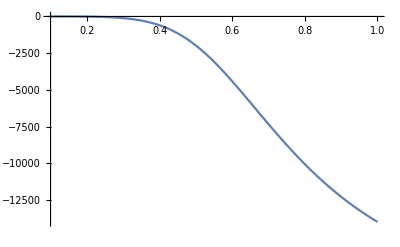

-Graphics-

```mathematica
Subscript[χ, DS] = -0.010;
Subscript[χ, DS] = Subscript[χ, DS];
c4=1;
c5= 0;
p=1;
q=0.5;
s=1;
Lambda=L
ConformalH=s1//PowerExpand//Simplify;
Chi = Xs1//PowerExpand//Simplify;
CovariantGalileon={p->1,q->0.5,s->1,φ'[a]->Sqrt[-Chi]/ConformalH,φ''[a]->PhiPP, ℋ[a]-> ConformalH,HconfP->D[ConformalH,a],HconfPP->D[D[ConformalH,a],a]};
LambdaCG=Omega/.DeSitterFP/.ȧ->ConformalH a/.CovariantGalileon/.Subscript[χ, DS]->0.5//PowerExpand//Simplify
LambdaCG/.a->1
LambdaCG/.a->0.1
Plot[Re[LambdaCG],{a,0.1,1}]
Plot[Im[LambdaCG],{a,0.1,1}]
```

```mathematica
ConformalH=s1//PowerExpand//Simplify
Chi = Xs1//PowerExpand//Simplify
Sqrt[-Chi]/ConformalH//PowerExpand//Simplify
PhiPP=D[%,a]//PowerExpand//Simplify
PhiPPP = D[%,a]//PowerExpand//Simplify
```

0.00223607 √((1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)

(167331. a^4.)/(1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))

((0.+182938. ⅈ) a^3.)/(1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))

((0.-182938. ⅈ) a^3. (30000.+(30000.+9.×10^8 a+1.11998×10^11 a^7)/(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8)))+(0.+548813. ⅈ) a^2. (1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8)))/(1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))^2

((1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8)) (((0.+91468.8 ⅈ) a^3. (30000.+9.×10^8 a+1.11998×10^11 a^7) (60000.+1.8×10^9 a+2.23997×10^11 a^7))/((1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8)^(3/2))-((0.+1.43421×10^17 ⅈ) a^3. (0.00114798+1. a^6))/(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))+(0.+1.09763×10^6 ⅈ) a^1. (1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8)))-2 (30000.+(30000.+9.×10^8 a+1.11998×10^11 a^7)/(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))) ((0.-182938. ⅈ) a^3. (30000.+(30000.+9.×10^8 a+1.11998×10^11 a^7)/(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8)))+(0.+548813. ⅈ) a^2. (1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))))/(1.+30000. a+1. √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))^3

DE eq. of state

```mathematica
s1=0.00223606797749979 √(1/a^2+30000./a+(√(1.+60000. a+9.*^8 a^2+2.79996*^10 a^8))/a^2)
Xs1 = 167330.81007393703 (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.*^8 a^2+2.79996*^10 a^8))/a^2)))^2.
s1o5 =Root[-1.680579953429951*^24 a^12+(-1./a^10-150000./a^9-(9.*^9)/a^8-(2.7*^14)/a^7-(4.05*^18)/a^6-(2.43*^22)/a^5) #1^2+(500000./a^8+(6.*^10)/a^7+(2.7*^15)/a^6+(5.4*^19)/a^5+(4.05*^23)/a^4) #1^4+(-(1.*^11)/a^6-(9.*^15)/a^5-(2.7*^20)/a^4-(2.7*^24)/a^3) #1^6+((1.*^16)/a^4+(6.*^20)/a^3+(9.*^24)/a^2) #1^8+(-(5.*^20)/a^2-(1.5*^25)/a) #1^10+1.*^25 #1^12&,2]
Xs1o5 = 10.824004689806106 (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.*^8 a^2+2.79996*^10 a^8))/a^2)))^(2/5)
```

0.00223607 √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)

167331. (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^2.

Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]

10.824 (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^(2/5)

```mathematica
(*SubstituteS0 = {H->s0 H0/a, X->XDS Xs0,s->0,p->0,q->0.5, Hdot-> s0 H0 a D[s0 H0/a,a], Xdot->XDS  s0 H0 D[Xs0,a]}*)
SubstituteS1 = {H->s1 H0/a,X->XDS Xs1,s->1,p->1,q->0.5, Hdot-> s1 H0  a D[s1 H0/a,a], Xdot->XDS  s1 H0 a D[Xs1,a]}
SubstituteS1o5 = {H->s1o5 H0/a,X->XDS Xs1o5,s->1/5,p->1,q->5/2, Hdot-> s1 H0  a D[s1o5 H0/a,a], Xdot->XDS  s1o5 H0 a D[Xs1o5,a]}
(*SubstituteS0p5 = {H->s0p5 H0/a, X->XDS Xs0p5,s->0.5,p->0.5,q->0.5, Hdot-> s0p5 H0 a D[s0p5 H0/a,a], Xdot-> XDS s0p5 H0 D[Xs0p5,a]};*)
```

{H→(0.00223607 √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2) H0)/a,X→167331. (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^2. XDS,s→1,p→1,q→0.5,Hdot→0.00223607 a √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2) H0 ((0.00111803 (-2/a^3-30000./a^2+(60000.+1.8×10^9 a+2.23997×10^11 a^7)/(2 a^2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))-(2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^3) H0)/(a √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2))-(0.00223607 √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2) H0)/a^2),Xdot→748.326 a (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^1. √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2) (-(a (-2/a^3-30000./a^2+(60000.+1.8×10^9 a+2.23997×10^11 a^7)/(2 a^2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))-(2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^3))/(2 (1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)^(3/2))+1/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2))) H0 XDS}

{H→1/a H0 Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2],X→10.824 (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^(2/5) XDS,s→1/5,p→1,q→5/2,Hdot→0.00223607 a √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2) H0 (-1/a^2 H0 Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]+(H0 (2.0167×10^25 a^11-(10./a^11+(1.35×10^6)/a^10+(7.2×10^10)/a^9+(1.89×10^15)/a^8+(2.43×10^19)/a^7+(1.215×10^23)/a^6) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^2-(-(4.×10^6)/a^9-(4.2×10^11)/a^8-(1.62×10^16)/a^7-(2.7×10^20)/a^6-(1.62×10^24)/a^5) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^4-((6.×10^11)/a^7+(4.5×10^16)/a^6+(1.08×10^21)/a^5+(8.1×10^24)/a^4) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^6-(-(4.×10^16)/a^5-(1.8×10^21)/a^4-(1.8×10^25)/a^3) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^8-((1.×10^21)/a^3+(1.5×10^25)/a^2) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^10))/(a (2 (-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]+4 (500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^3+6 (-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^5+8 ((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^7+10 (-(5.×10^20)/a^2-(1.5×10^25)/a) Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^9+1.2×10^26 Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]^11))),Xdot→1/((a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^(3/5))4.3296 a (-(a (-2/a^3-30000./a^2+(60000.+1.8×10^9 a+2.23997×10^11 a^7)/(2 a^2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))-(2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^3))/(2 (1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)^(3/2))+1/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2))) H0 XDS Root[-1.68058×10^24 a^12+(-1./a^10-150000./a^9-(9.×10^9)/a^8-(2.7×10^14)/a^7-(4.05×10^18)/a^6-(2.43×10^22)/a^5) #1^2+(500000./a^8+(6.×10^10)/a^7+(2.7×10^15)/a^6+(5.4×10^19)/a^5+(4.05×10^23)/a^4) #1^4+(-(1.×10^11)/a^6-(9.×10^15)/a^5-(2.7×10^20)/a^4-(2.7×10^24)/a^3) #1^6+((1.×10^16)/a^4+(6.×10^20)/a^3+(9.×10^24)/a^2) #1^8+(-(5.×10^20)/a^2-(1.5×10^25)/a) #1^10+1.×10^25 #1^12&,2]}

```mathematica
rhoDE = 120 H^2 χ^2 Subscript[F, 4][χ]-Subscript[G, 2][χ]-6 H^2 Subscript[G, 4][χ]+48 H^2 χ^3 Subscript[F, 4]'[χ]+2 χ Subscript[G, 2]'[χ]-6 √2 H χ^(3/2) Subscript[G, 3]'[χ]+24 H^2 χ Subscript[G, 4]'[χ]+24 H^2 χ^2 Subscript[G, 4]''[χ]
```

120 H^2 X^2 F4[X]-G2[X]-6 H^2 G4[X]+48 H^2 X^3 F4'[X]+2 X G2'[X]-6 √2 H X^(3/2) G3'[X]+24 H^2 X G4'[X]+24 H^2 X^2 G4''[X]

```mathematica
pDE = -24 H^2 χ^2 Subscript[F, 4][χ]-16 Ḣ χ^2 Subscript[F, 4][χ]-32 H χ χ̇ Subscript[F, 4][χ]+Subscript[G, 2][χ]+6 H^2 Subscript[G, 4][χ]+4 Ḣ Subscript[G, 4][χ]-16 H χ^2 χ̇ Subscript[F, 4]'[χ]+√2 √χ χ̇ Subscript[G, 3]'[χ]-12 H^2 χ Subscript[G, 4]'[χ]-8 Ḣ χ Subscript[G, 4]'[χ]-4 H χ̇ Subscript[G, 4]'[χ]-8 H χ χ̇ Subscript[G, 4]''[χ]
```

-24 H^2 X^2 F4[X]-16 Hdot X^2 F4[X]-32 H X Xdot F4[X]+G2[X]+6 H^2 G4[X]+4 Hdot G4[X]-16 H X^2 Xdot F4'[X]+√2 √X Xdot G3'[X]-12 H^2 X G4'[X]-8 Hdot X G4'[X]-4 H Xdot G4'[X]-8 H X Xdot G4''[X]

parametrize functions

```mathematica
c2 =.
c3=.
c4 =.
c5 =.

p =.
q =.
s =.

p2=p;
p3=p+q-1/2;
p4=p+2q;
p5=p+2q-2;

XDS =.

(*this X is for De Felice!!!!*)
XfromMyNotationToNJS = {X->-1/2X,XDS->-1/2XDS,Xdot->-1/2 Xdot}

G2[X]=-c2  X^p2 Hds^2 Subscript[m, p]^2 XDS^-p
G2'[X]=D[G2[X],X];
G2''[X]=D[G2'[X],X];
G3[X]=-c3 X^p3 Hds Subscript[m, p]^2 XDS^(-p-q)
G3'[X]=D[G3[X],X];
G3''[X]=D[G3'[X],X];
G4[X]=-c4 X^p4 XDS^(-p-2 q) Subscript[m, p]^2
Subscript[G, 4]'[X]=D[G4[X],X];
Subscript[G, 4]''[X]=D[ D[G4[X],X],X];
Derivative[3][Subscript[G, 4]][χ]=D[D[ Subscript[G, 4]'[X],X],X];
Subscript[F, 4][X]=c5 X^p5 XDS^(-p-2 q)Subscript[m, p]^2
Subscript[F, 4]'[X]= D[Subscript[F, 4][X],X];
Subscript[F, 4]''[X]=D[Subscript[F, 4]'[X],X];
```

{X→-X/2,XDS→-XDS/2,Xdot→-Xdot/2}

-c2 Hds^2 MPlanck^2 X^p XDS^-p

-c3 Hds MPlanck^2 X^(-1/2+p+q) XDS^(-p-q)

-c4 MPlanck^2 X^(p+2 q) XDS^(-p-2 q)

c5 MPlanck^2 X^(-2+p+2 q) XDS^(-p-2 q)

```mathematica
HdsSubstitution = {Hds-> H0 (OmegaDE0)^(1/(1+s)^2)}
DeSitterFP = {Subscript[c, 2]->3-6 Subscript[c, 4]-24 Subscript[c, 5]+12 Subscript[c, 4] p+24 Subscript[c, 4] q,Subscript[c, 3]->(√2 p)/(-1+2 p+2 q)-(4 √2 Subscript[c, 4] p)/(-1+2 p+2 q)-(16 √2 Subscript[c, 5] p)/(-1+2 p+2 q)+(8 √2 Subscript[c, 4] p^2)/(-1+2 p+2 q)-(4 √2 Subscript[c, 4] q)/(-1+2 p+2 q)-(16 √2 Subscript[c, 5] q)/(-1+2 p+2 q)+(24 √2 Subscript[c, 4] p q)/(-1+2 p+2 q)+(16 √2 Subscript[c, 4] q^2)/(-1+2 p+2 q)}
```

{Hds→H0 OmegaDE0^(1/(1+s)^2)}

{c2→3-6 c4-24 c5+12 c4 p+24 c4 q,c3→(√2 p)/(-1+2 p+2 q)-(4 √2 c4 p)/(-1+2 p+2 q)-(16 √2 c5 p)/(-1+2 p+2 q)+(8 √2 c4 p^2)/(-1+2 p+2 q)-(4 √2 c4 q)/(-1+2 p+2 q)-(16 √2 c5 q)/(-1+2 p+2 q)+(24 √2 c4 p q)/(-1+2 p+2 q)+(16 √2 c4 q^2)/(-1+2 p+2 q)}

```mathematica
XDS =.
rhoDE1=rhoDE/.XfromMyNotationToNJS/.HdsSubstitution/.DeSitterFP//Simplify;
pDE1=pDE/.XfromMyNotationToNJS/.HdsSubstitution/.DeSitterFP//Simplify;
OmegaDE0 = 1-OmegaM0-OmegaR0;
wDE =rhoDE1/pDE1//Simplify
```

-((3 X (-8 c5 (H (-X)^q-H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) (-XDS)^q) (H (1+2 p+4 q) (-X)^q-H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) (-1+2 p) (-XDS)^q)+2 c4 (-1+2 p+4 q) (H (-X)^q-H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) (-XDS)^q) (H (1+2 p+4 q) (-X)^q-H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) (-1+2 p) (-XDS)^q)+H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) (-2 H p (-X)^q+H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) (-1+2 p) (-XDS)^q) (-XDS)^q))/(-8 c5 (3 H^2 (-X)^(2 q) X+2 Hdot (-X)^(2 q) X+2 H (p+2 q) (-X)^(2 q) Xdot-H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) (2 p (-X)^q Xdot+2 q (-X)^q Xdot+3 H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) X (-XDS)^q) (-XDS)^q)+2 c4 (-1+2 p+4 q) (3 H^2 (-X)^(2 q) X+2 Hdot (-X)^(2 q) X+2 H (p+2 q) (-X)^(2 q) Xdot-H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) (2 p (-X)^q Xdot+2 q (-X)^q Xdot+3 H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) X (-XDS)^q) (-XDS)^q)-H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) (p (-X)^q Xdot+3 H0 (1-OmegaM0-OmegaR0)^(1/(1+s)^2) X (-XDS)^q) (-XDS)^q))

s  =  0

-0.849994

-0.99899

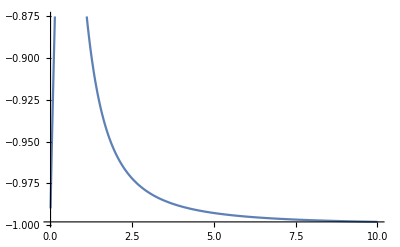

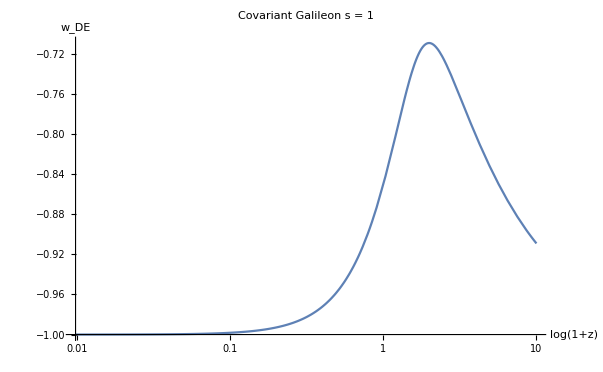

```mathematica
(*OmegaM0=0.3;
OmegaR0=10^(-5);
OmegaDE0 = 1-OmegaM0-OmegaR0;*)

(*XDS =-1;*)

(*c5 = 0;*)

wDEs2 =wDE/.SubstituteS1o5/.OmegaM0-> 0.3/.OmegaR0-> 10^(-5)/.c4-> -1/.c5->100/.XDS->-100/.s->1/5/.p->1/.q->5/2//Simplify;
wDEs1 =wDE/.SubstituteS1/.OmegaM0-> 0.3/.OmegaR0-> 10^(-5)/.c4-> -1/.c5->100/.XDS->-100/.s->1/.p->1/.q->0.5//Simplify;
wDEs1z=%/.a->1/zplus1;
(*rhoDEs0=rhoDE1/.SubstituteS0//PowerExpand//Simplify;
pDEs0=pDE1/.SubstituteS0//PowerExpand//Simplify;
wDEs0 =rhoDEs0/pDEs0/.s->1/.p->1/.q->0.5//Simplify;*)

a=1;
wDEs1
a=0.0010;
wDEs1
a=.


Plot[Re[wDEs1],{a,0.01,10}]
LogLinearPlot[Re[wDEs1z],{zplus1,0,10}, AxesLabel->{Style["log(1+z)",FontSize->20],Style["w_DE",FontSize->20]},PlotLabel->Style["Covariant Galileon s = 1", FontSize->25]]
```

-0.850347

-0.999439

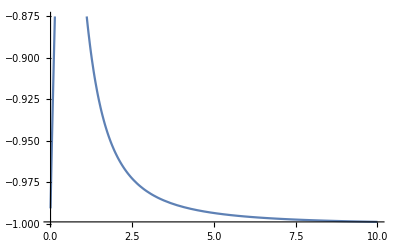

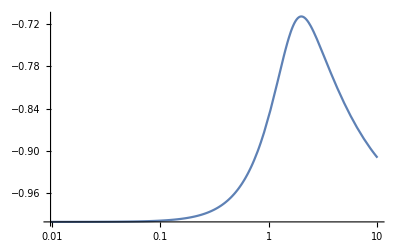

```mathematica
OmegaM0=0.3;
OmegaR0=10^(-4);
OmegaDE0 = 1-OmegaM0-OmegaR0;

(*XDS =-1;*)
c4 =20;
c5 = 0;


wDEs12 =wDE/.SubstituteS1/.XDS->-1/.s->1/.p->1/.q->0.5//Simplify;

(*rhoDEs0=rhoDE1/.SubstituteS0//PowerExpand//Simplify;
pDEs0=pDE1/.SubstituteS0//PowerExpand//Simplify;
wDEs0 =rhoDEs0/pDEs0/.s->1/.p->1/.q->0.5//Simplify;*)

a=1;
wDEs12
a=0.0010;
wDEs12
a=.

wDEs1z2=wDEs12/.a->1/zplus1;
Plot[Re[wDEs12],{a,0.01,10}]
LogLinearPlot[Re[wDEs1z2],{zplus1,0,10}]
c4=.
```

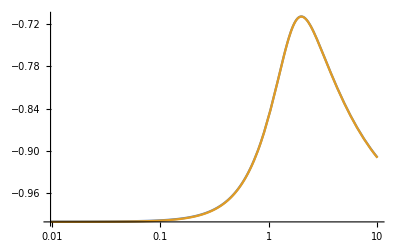

```mathematica
LogLinearPlot[{Re[wDEs1z],Re[wDEs1z2]},{zplus1,0,10}]
```

```mathematica
OmegaM0=.
OmegaR0=.
OmegaDE0=.
c4=.
```

```mathematica
XDS
```

-1

```mathematica
SubstituteS1
```

{H→(0.00223607 √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2) H0)/a,X→167331. (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^2. XDS,s→1,p→1,q→0.5,Hdot→0.00223607 √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2) H0 ((0.00111803 (-2/a^3-30000./a^2+(60000.+1.8×10^9 a+2.23997×10^11 a^7)/(2 a^2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))-(2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^3) H0)/(a √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2))-(0.00223607 √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2) H0)/a^2),Xdot→748.326 (a/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)))^1. √(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2) (-(a (-2/a^3-30000./a^2+(60000.+1.8×10^9 a+2.23997×10^11 a^7)/(2 a^2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))-(2 √(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^3))/(2 (1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2)^(3/2))+1/(√(1/a^2+30000./a+(√(1.+60000. a+9.×10^8 a^2+2.79996×10^10 a^8))/a^2))) H0 XDS}